```mathematica
mn = 0.939;

μ[mx_]:=mx/mn;
γ[ve_]:= 1/Sqrt[1 - ve^2]; (*natural units *)
p[ve_, mx_]:=γ[ve]*mx*ve;
s[mx_] :=(*2γ[0.6]*mx*mn+mx^2+mn^2;*)mx^2/μ[mx]^2*(1+μ[mx]^2+2/(√0.3)*μ[mx]);
Er[ctheta_,ve_, mx_]:= (mn*mx^2*γ[ve]^2*ve^2)/(mn^2 + mx^2 + 2*γ[ve]*mx*mn)*(1 - ctheta);
```

```mathematica
σTot[dσ_, mx_]:= Integrate[dσ[t,mx](**1/(2*p[0.6, mx]^2)*)* 0.3*((1+μ[mx]^2+2/(√0.3)*μ[mx])/(2*(1-0.3)*mx^2)),{t,-4 p[0.6, mx]^2(*-4*mx^2*((1-0.3)/(0.3*(1+μ[mx]^2+2/(√0.3)*μ[mx])))*),0}];
```

## Differential Cross Sections

```mathematica
d1[t_,mx_]:= (mn^2*(4*mx^2-t)*(4*mx^2-μ[mx]^2*t))/(32*π*(μ[mx])^2*s[mx]);
d2[t_, mx_]:= (mn^2*t*(μ[mx]^2*t - 4*mx^2))/(32*π*s[ mx]);
d3[t_, mx_]:= (mn^2*t*(t - 4*mx^2))/(32*π*s[ mx]);
d4[t_, mx_]:= (mn^2*t^2)/(32*π*s[mx]);
d5[t_,mx_]:= (2*(μ[mx]^2+1)^2*mx^4-4*(μ[mx]^2+1)*μ[mx]^2*s[ mx]*mx^2+μ[mx]^4*(2*s[ mx]^2+2*s[ mx]*t+t^2))/(16*π*μ[mx]^4*s[ mx]);
d6[t_, mx_]:= 1/(16*π*μ[mx]^4*s[mx])(2*(μ[mx]^2-1)^2*mx^4-4*(μ[mx]^2*s[mx] +s[ mx]+μ[mx]^2*t)*μ[mx]^2*mx^2+μ[mx]^4*(2*s[ mx]^2+2*s[ mx]*t+t^2));
d7[t_, mx_]:= 1/(16*π*μ[mx]^4*s[mx])(2*(μ[mx]^2-1)^2*mx^4-4*(μ[mx]^2*s[mx] +s[mx]+t)*μ[mx]^2*mx^2+μ[mx]^4*(2*s[mx]^2+2*s[mx]*t+t^2));
```

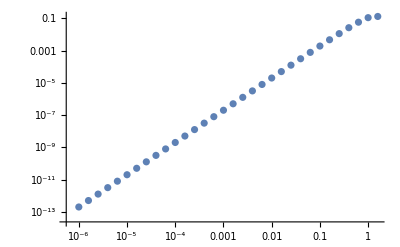

```mathematica
ListLogLogPlot[Evaluate@Table[ With[{x := 10^xp}, Table[{x,σTot[thing, x]}, {xp, -6, 6, 0.2}]], {thing, {d7}}]]
```

```mathematica
With[{x := 10^xp}, Table[{x,σTot[d7, x]}, {xp, -6, 6, 0.2}]]
```

{{1.×10^-6,2.00634×10^-13},{1.58489×10^-6,5.03962×10^-13},{2.51189×10^-6,1.2659×10^-12},{3.98107×10^-6,3.17979×10^-12},{6.30957×10^-6,7.98726×10^-12},{0.00001,2.0063×10^-11},{0.0000158489,5.03959×10^-11},{0.0000251189,1.26588×10^-10},{0.0000398107,3.17974×10^-10},{0.0000630957,7.98706×10^-10},{0.0001,2.00623×10^-9},{0.000158489,5.03929×10^-9},{0.000251189,1.26576×10^-8},{0.000398107,3.17926×10^-8},{0.000630957,7.98516×10^-8},{0.001,2.00547×10^-7},{0.00158489,5.03629×10^-7},{0.00251189,1.26457×10^-6},{0.00398107,3.17449×10^-6},{0.00630957,7.96618×10^-6},{0.01,0.0000199791},{0.0158489,0.0000500618},{0.0251189,0.000125257},{0.0398107,0.000312668},{0.0630957,0.000777549},{0.1,0.00192177},{0.158489,0.00470165},{0.251189,0.0113045},{0.398107,0.0263489},{0.630957,0.0578218},{1.,0.110587},{1.58489,0.131241},{2.51189,-0.307838},{3.98107,-3.65261},{6.30957,-22.7921},{10.,-125.054},{15.8489,-669.814},{25.1189,-3639.65},{39.8107,-20348.2},{63.0957,-117266.},{100.,-693842.},{158.489,-4.19005×10^6},{251.189,-2.56786×10^7},{398.107,-1.58972×10^8},{630.957,-9.90835×10^8},{1000.,-6.20296×10^9},{1584.89,-3.89434×10^10},{2511.89,-2.4494×10^11},{3981.07,-1.54237×10^12},{6309.57,-9.71941×10^12},{10000.,-6.12763×10^13},{15848.9,-3.86432×10^14},{25118.9,-2.43744×10^15},{39810.7,-1.53761×10^16},{63095.7,-9.70044×10^16},{100000.,-6.12008×10^17},{158489.,-3.86131×10^18},{251189.,-2.43624×10^19},{398107.,-1.53714×10^20},{630957.,-9.69855×10^20},{1.×10^6,-6.11932×10^21}}

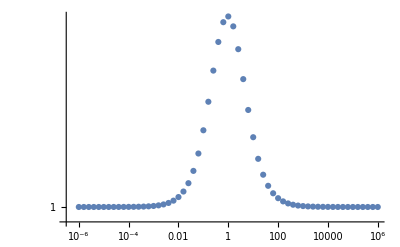

```mathematica
ListLogLogPlot[ With[{x := 10^xp}, Table[{x,(x^2/μ[x]^2*(1+μ[x]^2+2/(√0.3)*μ[x]))/(2γ[0.6]*x*mn+x^2+mn^2)}, {xp, -6, 6, 0.2}]]]
```